Biological Modelling and Model Analysis - day III

Analysis of ordinary differential equation
 and recurrence equation models

Sander van Doorn

Groningen Institute for Evolutionary Life Sciences

g.s.van.doorn@rug.nl

## Ex. III-1 The Collins genetic toggle switch

The model equations:

```mathematica
eqX=D[X[t],t]==5/(1+Y[t]^4)-X[t];
eqY=D[Y[t],t]==5/(1+X[t]^4)-Y[t];
```

Q(a): Give a biological interpretation of the equations.

The two transcription factors are under mutual regulatory control: gene X is transcribed if the concentration of Y is low; gene Y is transcribed if the concentration of X is low; both transcription factors decay at a constant per capita rate.

Q(b): Study the system by phase-space analysis, and determine the stability of the equilibria graphically

The plot below shows the null-isoclines and the vector field. There are three intersection points of the null clines. Two equilibria are located at the boundaries of the state space, and there is an equilibrium in the middle. The vector field indicates that the middle equilibrium is a saddle point. Its stable manifold separates between the basins of attraction of the boundary equilibria, which are both stable.

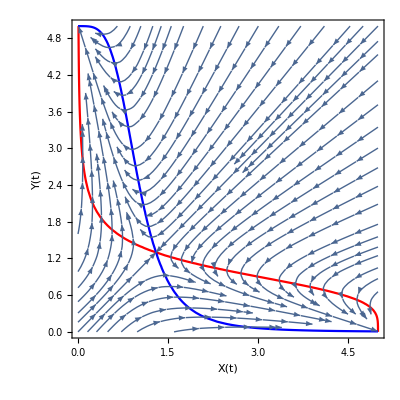

```mathematica
pl1=ContourPlot[eqX[[2]]==0,{X[t],0,5},{Y[t],0,5},ContourStyle->Red,FrameLabel->{X[t],Y[t]}];
pl2=ContourPlot[eqY[[2]]==0,{X[t],0,5},{Y[t],0,5},ContourStyle->Blue];
pl3=StreamPlot[{eqX[[2]],eqY[[2]]},{X[t],0,5},{Y[t],0,5}];
Show[{pl1,pl2,pl3}]
```

Q(c): Check your results with a mathematical stability analysis.

```mathematica
equilibrium1=FindRoot[{eqX[[2]]==0.0,eqY[[2]]==0.0},{{X[t],1},{Y[t],1}}]
equilibrium2=FindRoot[{eqX[[2]]==0.0,eqY[[2]]==0.0},{{X[t],0},{Y[t],5}}]
equilibrium3=FindRoot[{eqX[[2]]==0.0,eqY[[2]]==0.0},{{X[t],5},{Y[t],0}}]
```

{X[t]→1.29915,Y[t]→1.29915}

{X[t]→0.00798722,Y[t]→5.}

{X[t]→5.,Y[t]→0.00798722}

```mathematica
J=D[{eqX[[2]],eqY[[2]]},{{X[t],Y[t]}}]
```

{{-1,-(20 Y[t]^3)/((1+Y[t]^4)^2)},{-(20 X[t]^3)/((1+X[t]^4)^2),-1}}

```mathematica
Eigenvalues[J/.equilibrium1]
Eigenvalues[J/.equilibrium2]
Eigenvalues[J/.equilibrium3]
```

{-3.96068,1.96068}

{-1.00025,-0.999745}

{-1.00025,-0.999745}

Q(d): Explain why the system behaves as a bistable switch

As long as the concentrations of the two transcription factors are approximately equal, small perturbations of the concentrations can push the system towards either one of the stable boundary equilibria (one transcription factor ON, the other OFF). However, once the system has reached a stable state, it cannot easily be pushed to the alternative attractor any more.

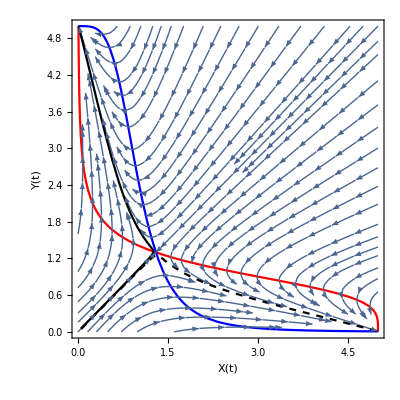

```mathematica
sol1=NDSolve[{eqX,eqY,X[0]==0.05,Y[0]==0.055},{X[t],Y[t]},{t,0,10}]//First;
pl4=ParametricPlot[{X[t],Y[t]}/.sol1,{t,0,10},PlotStyle->Black];
sol2=NDSolve[{eqX,eqY,X[0]==0.055,Y[0]==0.05},{X[t],Y[t]},{t,0,10}]//First;
pl5=ParametricPlot[{X[t],Y[t]}/.sol2,{t,0,10},PlotStyle->{Black,Dashed}];
Show[{pl1,pl2,pl3,pl4,pl5}]
```

## Ex. III-2 Glycolytic oscillations

The model equations:

```mathematica
eqS=D[S[t],t]==i-c S[t] P[t]^2;
eqP=D[P[t],t]==c S[t] P[t]^2-k P[t];
```

Q(a,b): ...how many ADP are necessary to activate the enzyme? What implicit assumption has been made in the model to motivate this simplification?

Under the assumption of mass-action kinetics, the term c S P^2represents the rate of a process that relies on the interaction between substrate (F6P) and two molecules of ADP. Normally, you would also expect to see the concentrations of the enzyme en the substrate ATP as factors in the mass action term (rate ∝ S P^2 [FBP] [PFK]), but these concentrations are considered to be constant, so that they can be absorbed in the parameter c.

Q(c): Study the system graphically, and attempt to predict its behaviour for the parameters I=1, k=1 and c=0.9.

The plot below shows the null-isoclines and the vector field. There is a single intersection point of the null clines. The equilibrium appears to be a spiral, but its stability is difficult to assess from the vector field

```mathematica
pars={i->1, k->1,c->0.9};
```

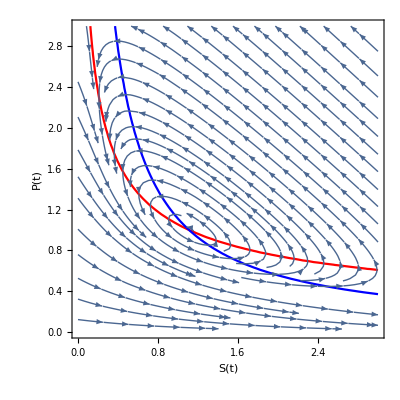

```mathematica
pl1=ContourPlot[Evaluate[eqS[[2]]/.pars]==0,{S[t],0,3},{P[t],0,3},ContourStyle->Red,FrameLabel->{S[t],P[t]}];
pl2=ContourPlot[Evaluate[eqP[[2]]/.pars]==0,{S[t],0,3},{P[t],0,3},ContourStyle->Blue];
pl3=StreamPlot[{eqS[[2]],eqP[[2]]}/.pars,{S[t],0,3},{P[t],0,3}];
Show[{pl1,pl2,pl3}]
```

Q(c): Check your predictions by means of a mathematical stability analysis and numerical simulations.

```mathematica
equilibrium=FindRoot[{eqS[[2]]==0.0,eqP[[2]]==0.0}/.pars,{{S[t],1},{P[t],1}}]
```

{S[t]→1.11111,P[t]→1.}

```mathematica
J=D[{eqS[[2]],eqP[[2]]},{{S[t],P[t]}}]/.pars/.equilibrium
```

{{-0.9,-2.},{0.9,1.}}

```mathematica
Eigenvalues[J]
```

{0.05+0.947365 ⅈ,0.05-0.947365 ⅈ}

The local stability analysis indicates that the equilibrium is an unstable spiral

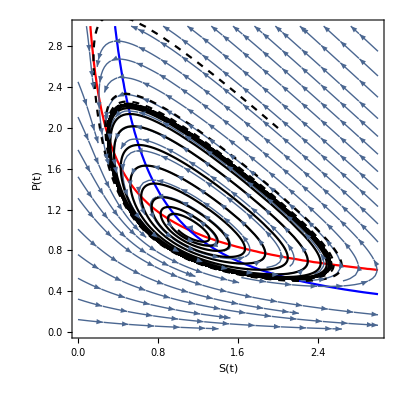

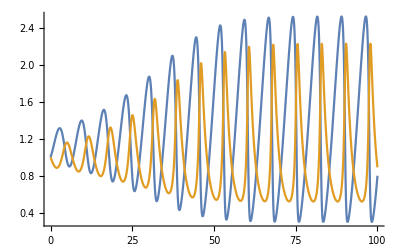

```mathematica
sol1=NDSolve[{eqS,eqP,S[0]==1,P[0]==1}/.pars,{S[t],P[t]},{t,0,100}]//First;
pl4=ParametricPlot[{S[t],P[t]}/.sol1,{t,0,100},PlotStyle->Black];
sol2=NDSolve[{eqS,eqP,S[0]==2,P[0]==2}/.pars,{S[t],P[t]},{t,0,100}]//First;
pl5=ParametricPlot[{S[t],P[t]}/.sol2,{t,0,100},PlotStyle->{Dashed, Black}];
Show[{pl1,pl2,pl3,pl4,pl5}]
Plot[Evaluate[{S[t],P[t]}/.sol1],{t,0,100}]
```

The simulations indicate that the unstable spiral point is surrounded by a stable limit cycle

## Ex. III-3 Stability in discretised ODEs

The recurrence equations for the discretisation of the ODE model are

```mathematica
eqx=x+δ f[x,y]
eqy=y+δ g[x,y]
```

x+δ f[x,y]

y+δ g[x,y]

Compute the Jacobian of the recurrence equation system:

```mathematica
JR=D[{eqx,eqy},{{x,y}}]
```

{{1+δ f^(1,0)[x,y],δ f^(0,1)[x,y]},{δ g^(1,0)[x,y],1+δ g^(0,1)[x,y]}}

```mathematica
TrR=Tr[JR]
DetR=Det[JR]
```

2+δ g^(0,1)[x,y]+δ f^(1,0)[x,y]

1+δ g^(0,1)[x,y]+δ f^(1,0)[x,y]+δ^2 g^(0,1)[x,y] f^(1,0)[x,y]-δ^2 f^(0,1)[x,y] g^(1,0)[x,y]

Compute the Jacobian of the associated ODE system:

```mathematica
JD=D[{f[x,y],g[x,y]},{{x,y}}]
```

{{f^(1,0)[x,y],f^(0,1)[x,y]},{g^(1,0)[x,y],g^(0,1)[x,y]}}

```mathematica
TrODE=Tr[JD]
DetODE=Det[JD]
```

g^(0,1)[x,y]+f^(1,0)[x,y]

g^(0,1)[x,y] f^(1,0)[x,y]-f^(0,1)[x,y] g^(1,0)[x,y]

Now we can observe that the traces and determinants are related in the following ways:

```mathematica
TrR==2+δ TrODE//Simplify
DetR==1+δ TrODE+δ^2 DetODE//Simplify
```

True

True

Assuming that δ is small, the recurrence equation is stable when

|Tr(J_R)|<1+det(J_R)<2 ⇔
 |2+δ Tr(J_ODE)|<1+1+δ Tr(J_ODE)+δ^2 det(J_ODE)<2 ⇔
|2+δ Tr(J_ODE)|-2<δ Tr(J_ODE)+δ^2 det(J_ODE)<0 ⇔
δ Tr(J_ODE)<δ Tr(J_ODE)+δ^2 det(J_ODE)<0 ⇔det(J_ODE)>0 ⋀Tr(J_ODE)<-δ det(J_ODE)

i.e., when the ODE system has a positive determinant and a trace that is a little bit below zero. These are almost exactly identical to the stability conditions for the ODE system. For the stability of the two systems to coincide, we obtain the following upper limit for the integration stepsize:

δ<-(Tr(J_ODE))/(det(J_ODE))